## This Mathematica notebook processes data from computer simulations and generates Figures 3 and S3EF

### Run all cells sequentially unless only a specific figure is required but in such a case please note that some previous cells must also be executed.

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["ErrorBarPlots`"]
Needs["ErrorBarLogPlots`"] (* this has to be installed separately*)
Clear[SE]
SE[x_]:=If[Length[x]>1,Sqrt[Variance[x]/Length[x]],0]
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

### Functions for drawing snapshots of simulated biofilms:

```mathematica
Clear[FrontExample];
FrontExample[name_]:=Module[{str,nn,what,data,ymin,ymax,bn,tmp,ww,color},
If[FileExistsQ[name]==False,Print["file not found"];Interrupt[]];
str=OpenRead[name];
tmp=Read[str,{Number,Number,Number,Number,Number}];
nn=tmp[[1]];
ww=tmp[[4]];
what=Table[Number,{i,13}];
data=Table[Read[str,what],{i,nn}];
Close[str];
(*Do[data[[i,1]]=i,{i,Length[data]}];*)
ymin=Min[-data[[All,5]]]-3;ymax=Max[-data[[All,5]]]+3;
SeedRandom[1234];
If[Max[data[[All,1]]]<=1,color={Green,Red},color=Table[Hue[RandomReal[],0.25+0.75RandomReal[],1],{i,Max[data[[All,1]]]+1}]];
Graphics[Flatten[{Thickness->0.8/ww,CapForm->"Round",Table[{color[[1+data[[i,1]]]],Line[{{x+d Cos[ϕ],-y-d Sin[ϕ]},{x-d Cos[ϕ],-y+d Sin[ϕ]}}/.{x->data[[i,4]],y->data[[i,5]],ϕ->data[[i,10]],d->data[[i,12]]}]},{i,Length[data]}]}],ImageSize->600,PlotRange->{{-ww/2,ww/2},{ymin,ymax}},Background->Black]
]

Clear[ColonyFrames];
ColonyFrames[name_]:=Module[{data,ymin,ymax,bn,tmp},
data=ReadList[name,Table[Number,{i,4+13}]];
SplitBy[data,(#[[1]])&]
]
Clear[DrawFrame];
DrawFrame[data_]:=Module[{ww=100,ymin,ymax,data1,data0,color},
ymin=Min[-data[[All,4+5]]]-3;ymax=Max[-data[[All,4+5]]]+3;
SeedRandom[1234];
If[Max[data[[All,5]]]==1,color={Green,Red},color=Table[Hue[RandomReal[],0.25+0.75RandomReal[],1],{i,Max[data[[All,5]]]+1}]];
Graphics[Flatten[{Thickness->0.8/ww,CapForm->"Round",Table[{color[[1+data[[i,5]]]],Line[{{x+d Cos[ϕ],-y-d Sin[ϕ]},{x-d Cos[ϕ],-y+d Sin[ϕ]}}/.{x->data[[i,4+4]],y->data[[i,4+5]],ϕ->data[[i,4+10]],d->data[[i,4+12]]}]},{i,Length[data]}]}],ImageSize->600,PlotRange->{{-ww/2,ww/2},{ymin,ymax}},Background->Black]
]
```

## Fig. 3 A

73

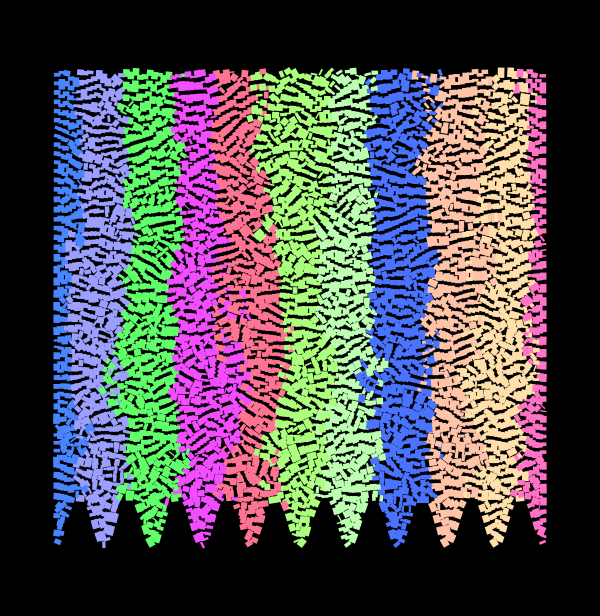

```mathematica
frames=ColonyFrames[NotebookDirectory[]<>"data_Fig_3\\positions_3A.dat"];
Length[frames]
DrawFrame[frames[[-1]]]
```

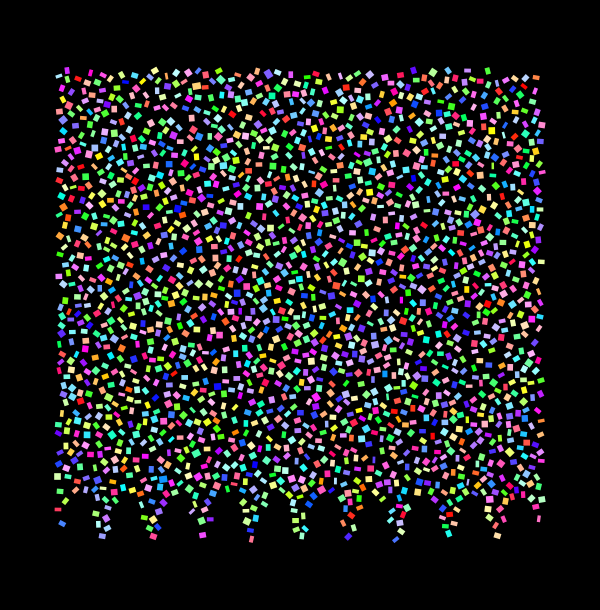

```mathematica
DrawFrame[frames[[1]]]
```

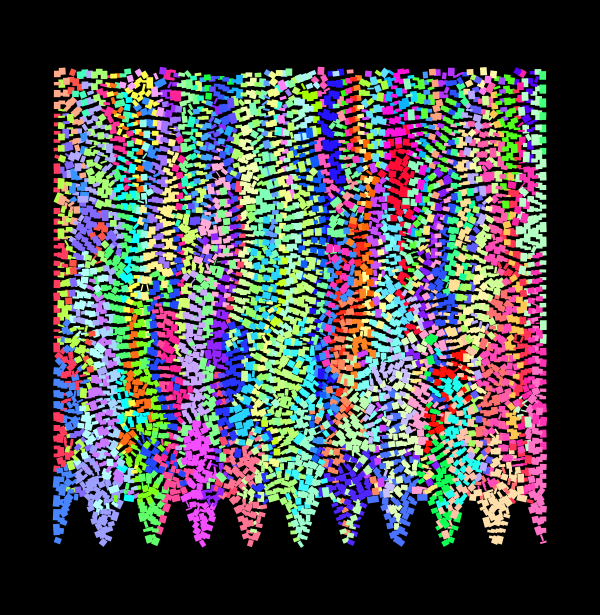

```mathematica
DrawFrame[frames[[10]]]
```

## Fig. 3 B

### helper functions for loading and processing files containing the number of bacteria of each type (allele) versus time

```mathematica
Clear[AllelesEndPoint,AllelesAllTimes]
AllelesEndPoint[name_]:=Module[{names,frames,secsizes},names=FileNames[NotebookDirectory[]<>"data_Fig_3\\"<>name<>"\\types_*.dat"];
frames=Table[Gather[ReadList[names[[i]],{Number,Number,Number,Number}],(#1[[1]]==#2[[1]])&],{i,Length[names]}];Print[Length[frames]," ",Length[#]&/@frames];
frames=Select[frames,(Length[#]>70)&];(* select only runs that have finished *)
secsizes=Table[1.frames[[i,-1,All,4]],{i,Length[frames]}];
{Mean[1.Length[#]&/@secsizes],SE[1.Length[#]&/@secsizes],Mean[Flatten[secsizes]]/Mean[Total[#]&/@(secsizes)],SE[Flatten[1.secsizes]]/Mean[Total[#]&/@(secsizes)]}
]
AllelesAllTimes[name_]:=Module[{names,frames,secsizes},names=FileNames[NotebookDirectory[]<>"data_Fig_3\\"<>name<>"\\types_*.dat"];
frames=Table[Gather[ReadList[names[[i]],{Number,Number,Number,Number}],(#1[[1]]==#2[[1]])&],{i,Length[names]}];Print[Length[frames]," ",Length[#]&/@frames];
frames=Select[frames,(Length[#]>70)&];(* select only runs that have finished *)
Table[secsizes=Table[1.frames[[i,j,All,4]],{i,Length[frames]}];
{j,Mean[1.Length[#]&/@secsizes],SE[1.Length[#]&/@secsizes],Mean[Flatten[secsizes]]/Mean[Total[#]&/@(secsizes)],SE[Flatten[1.secsizes]]/Mean[Total[#]&/@(secsizes)]},
{j,Min[Length[#]&/@frames]}]
]
```

```mathematica
datasetnames={"100x110_no_adh_shorter_10reps_multtypes_P5_A5","100x110_no_adh_shorter_10reps_multtypes_P10_A5",
"100x110_no_adh_shorter_10reps_multtypes_P20_A5","100x110_no_adh_shorter_10reps_multtypes_P50_A5","100x110_no_adh_shorter_10reps_multtypes_P50_A0"};
allSecs=Table[{{#[[1]],#[[2]]},ErrorBar[#[[3]]]}&/@AllelesAllTimes[datasetnames[[i]]][[1;;,{1,2,3}]],{i,Length[datasetnames]}];
```

5 {73,73,73,73,47}

5 {73,73,73,73,62}

10 {72,72,72,72,73,72,72,72,73,9}

9 {73,72,72,72,72,72,72,73,71}

7 {72,73,73,73,72,73,42}

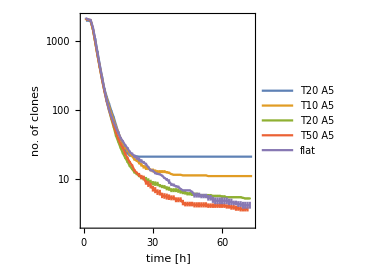

```mathematica
ErrorListLogPlot[allSecs,Joined->True,PlotRange->All,Frame->True,FrameLabel->{"time [h]","no. of clones"},PlotLegends->{"T20 A5","T10 A5","T20 A5","T50 A5","flat"},BaseStyle->FontSize->20,AspectRatio->1,ImageSize->270]
```

## Fig. 3 C, D

```mathematica
datasetnames={"100x110_no_adh_shorter_10reps_multtypes_P50_A0","100x110_no_adh_shorter_10reps_multtypes_P50_A5","100x110_no_adh_shorter_10reps_multtypes_P50_A2","100x110_no_adh_shorter_10reps_multtypes_P20_A5","100x110_no_adh_shorter_10reps_multtypes_P20_A2","100x110_no_adh_shorter_10reps_multtypes_P10_A5","100x110_no_adh_shorter_10reps_multtypes_P10_A2","100x110_no_adh_shorter_10reps_multtypes_P5_A5","100x110_no_adh_shorter_10reps_multtypes_P5_A2"};
(* check if all data sets exist *)
lens=Length[FileNames[NotebookDirectory[]<>"data_Fig_3\\"<>#<>"\\types_*.dat"]]&/@datasetnames;
Do[If[lens[[i]]==0,Print["missing data set: ",datasetnames[[i]]];Interrupt[]],{i,Length[datasetnames]}]
```

```mathematica
allsTA3=AllelesEndPoint[#]&/@datasetnames
```

7 {72,73,73,73,72,73,42}

9 {73,72,72,72,72,72,72,73,71}

7 {73,72,72,72,73,72,41}

10 {72,72,72,72,73,72,72,72,73,9}

6 {73,72,73,73,73,68}

5 {73,73,73,73,62}

6 {73,73,73,73,73,12}

5 {73,73,73,73,47}

5 {73,73,73,73,24}

{{4.16667,0.477261,0.24,0.0316548},{3.66667,0.288675,0.272727,0.0300285},{3.,0.,0.333333,0.0369014},{5.22222,0.146986,0.191489,0.00427687},{5.6,0.6,0.178571,0.00957261},{11.,0.,0.0909091,0.00381939},{11.4,0.244949,0.0877193,0.00462274},{21.,0.,0.047619,0.00122963},{20.,0.408248,0.05,0.00202703}}

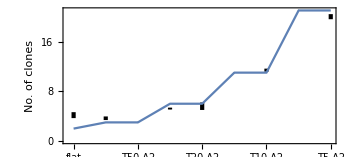

```mathematica
Show[ErrorListPlot[allsTA3[[All,1;;2]],PlotRange->All,BaseStyle->{FontSize->18},PlotStyle->{Black,AbsolutePointSize[1],AbsoluteThickness[3]},Frame->True,FrameLabel->{None,"No. of clones"},FrameTicks->{{Automatic,None},{Table[{i,If[i!=1,Rotate[(("T"<>#[[1]]<>" A"<>#[[2]])&/@StringCases[datasetnames[[i]],"_P"~~t__~~"_A"~~a__->{t,a}])[[1]],π/4],Rotate["flat    ",π/4]]},{i,Length[datasetnames]}],None}},ImageSize->350,AspectRatio->0.45],ListPlot[MapIndexed[{#2[[1]],(100+#1)/#1}&,{100,50,50,20,20,10,10,5,5}],Joined->True]]
```

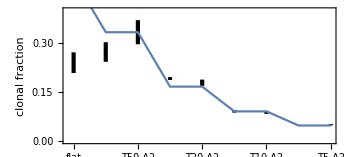

```mathematica
Show[ErrorListPlot[allsTA3[[All,{3,4}]],PlotRange->{All,{0,0.4}},BaseStyle->{FontSize->18},PlotStyle->{Black,AbsolutePointSize[1],AbsoluteThickness[3]},Frame->True,FrameLabel->{None,"clonal fraction"},FrameTicks->{{Automatic,None},{Table[{i,If[i!=1,Rotate[(("T"<>#[[1]]<>" A"<>#[[2]])&/@StringCases[datasetnames[[i]],"_P"~~t__~~"_A"~~a__->{t,a}])[[1]],π/4],Rotate["flat    ",π/4]]},{i,Length[datasetnames]}],None}},ImageSize->350,AspectRatio->0.45],ListPlot[MapIndexed[{#2[[1]],#1/(100+#1)}&,{100,50,50,20,20,10,10,5,5}],Joined->True]]
```

## Fig. 3 E

```mathematica
tmp={(AllelesEndPoint[#]&/@{"100x110_no_adh_shorter_10reps_multtypes_P5_A0","100x110_no_adh_shorter_10reps_multtypes_P5_A0.5","100x110_no_adh_shorter_10reps_multtypes_P5_A1","100x110_no_adh_shorter_10reps_multtypes_P5_A2","100x110_no_adh_shorter_10reps_multtypes_P5_A5"}),(AllelesEndPoint[#]&/@{"100x110_no_adh_shorter_10reps_multtypes_P10_A0","100x110_no_adh_shorter_10reps_multtypes_P10_A0.5","100x110_no_adh_shorter_10reps_multtypes_P10_A1","100x110_no_adh_shorter_10reps_multtypes_P10_A2","100x110_no_adh_shorter_10reps_multtypes_P10_A5"}),(AllelesEndPoint[#]&/@{"100x110_no_adh_shorter_10reps_multtypes_P20_A0","100x110_no_adh_shorter_10reps_multtypes_P20_A0.5","100x110_no_adh_shorter_10reps_multtypes_P20_A1","100x110_no_adh_shorter_10reps_multtypes_P20_A2","100x110_no_adh_shorter_10reps_multtypes_P20_A5"}),(AllelesEndPoint[#]&/@{"100x110_no_adh_shorter_10reps_multtypes_P50_A0","100x110_no_adh_shorter_10reps_multtypes_P50_A0.5","100x110_no_adh_shorter_10reps_multtypes_P50_A1","100x110_no_adh_shorter_10reps_multtypes_P50_A2","100x110_no_adh_shorter_10reps_multtypes_P50_A5"})}[[All,All,1;;2]]
```

6 {73,73,72,72,73,59}

9 {73,72,73,73,72,73,72,73,17}

5 {72,73,73,73,52}

5 {73,73,73,73,24}

5 {73,73,73,73,47}

7 {72,73,73,73,72,73,27}

10 {73,72,72,73,73,72,72,72,72,72}

8 {72,73,72,72,72,72,73,11}

6 {73,73,73,73,73,12}

5 {73,73,73,73,62}

7 {72,73,73,73,72,73,23}

10 {72,72,72,72,73,72,72,73,73,73}

8 {72,73,72,73,73,72,72,26}

6 {73,72,73,73,73,68}

10 {72,72,72,72,73,72,72,72,73,9}

7 {72,73,73,73,72,73,42}

10 {72,72,73,72,72,72,72,72,73,73}

7 {72,73,73,72,72,73,67}

7 {73,72,72,72,73,72,41}

9 {73,72,72,72,72,72,72,73,71}

{{{4.8,0.489898},{9.,0.654654},{16.,0.816497},{20.,0.408248},{21.,0.}},{{4.16667,0.477261},{6.2,0.38873},{9.,0.308607},{11.4,0.244949},{11.,0.}},{{4.16667,0.477261},{3.9,0.276887},{4.28571,0.359516},{5.6,0.6},{5.22222,0.146986}},{{4.16667,0.477261},{4.4,0.221108},{3.16667,0.166667},{3.,0.},{3.66667,0.288675}}}

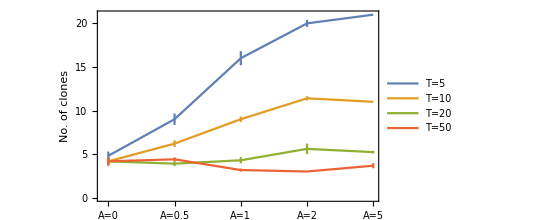

```mathematica
ErrorListPlot[tmp,PlotRange->All,Joined->True,BaseStyle->{FontSize->18},Frame->True,FrameLabel->{None,"No. of clones"},FrameTicks->{{Automatic,None},{{{1,"A=0"},{2,"A=0.5"},{3,"A=1"},{4,"A=2"},{5,"A=5"}},None}},ImageSize->{Automatic,150},AspectRatio->0.55,PlotLegends->{"T=5","T=10","T=20","T=50"}]
```

## Fig. 3 F

### this function loads a file containing positions of bacteria at different times

```mathematica
Clear[CellsPositions];
CellsPositions[name_]:=Module[{data,ymin,ymax,bn,tmp,cells,j},
data=ReadList[name,Table[Number,{i,4+13}]];
data=Select[data,(#[[1]]>20)&]; (* select only later trajectories when s.s. has been reached *)
cells=GatherBy[data,(#[[3]])&][[1;;]];
Table[{#[[8]],#[[9]]}&/@cells[[i]],{i,Length[cells]}]
]
cells=CellsPositions[NotebookDirectory[]<>"data_Fig_3\\100x110_no_adh_shorter_10reps_P50_A0\\positions_1_0.dat"];
Length[cells]
```

120127

### plot for a flat - bottom well:

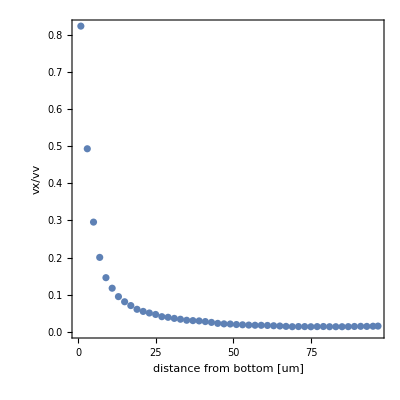

```mathematica
pl1=ErrorListPlot[Module[{tmp,tmp2,maxy=Max[cells[[All,All,2]]]},tmp=Flatten[Select[Table[Table[{maxy-cells[[i,j+1,2]],Abs[cells[[i,j+1,1]]-cells[[i,j,1]]]/Norm[cells[[i,j+1]]-cells[[i,j]]]},{j,Length[cells[[i]]]-1}],{i,Length[cells]}],(Length[#]>0)&],1];
tmp2=Gather[tmp,(Floor[#1[[1]]/2]==Floor[#2[[1]]/2])&];
{{Mean[#[[All,1]]],Mean[#[[All,2]]]},ErrorBar[SE[#[[All,2]]]]}&/@tmp2
],PlotRange->All,Frame->True,FrameLabel->{"distance from bottom [um]","vx/vv"},Axes->False,AspectRatio->1,BaseStyle->{FontSize->18}]
```

```mathematica
cells=CellsPositions[NotebookDirectory[]<>"data_Fig_3\\100x110_no_adh_shorter_10reps_P10_A5\\positions_1_0.dat"];
Length[cells]
```

119479

### plot for a corrugated - bottom well:

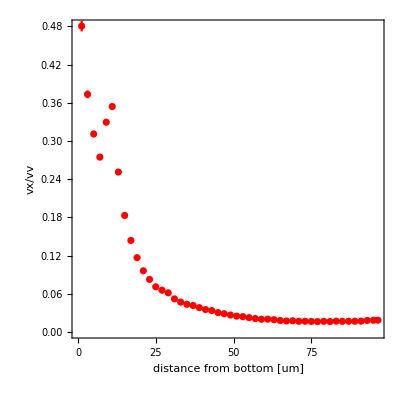

```mathematica
pl2=ErrorListPlot[Module[{tmp,tmp2,maxy=Max[cells[[All,All,2]]]},tmp=Flatten[Select[Table[Table[{maxy-cells[[i,j+1,2]],Abs[cells[[i,j+1,1]]-cells[[i,j,1]]]/Norm[cells[[i,j+1]]-cells[[i,j]]]},{j,Length[cells[[i]]]-1}],{i,Length[cells]}],(Length[#]>0)&],1];
tmp2=Gather[tmp,(Floor[#1[[1]]/2]==Floor[#2[[1]]/2])&];
{{Mean[#[[All,1]]],Mean[#[[All,2]]]},ErrorBar[SE[#[[All,2]]]]}&/@tmp2
],PlotRange->All,PlotStyle->Red,Frame->True,FrameLabel->{"distance from bottom [um]","vx/vv"},Axes->False,AspectRatio->1,BaseStyle->{FontSize->18}]
```

### final, combined plot :

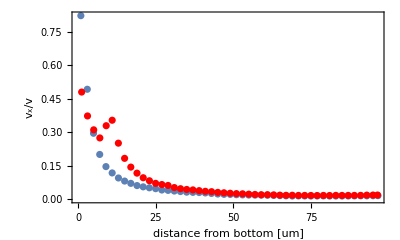

```mathematica
Show[pl1,pl2,BaseStyle->FontSize->18,AspectRatio->0.6,FrameLabel->{"distance from bottom [um]","v_x/v"},ImageSize->{Automatic,170}]
```

## Fig. 3 G

### fixation probabilities obtained from the simulation. This was obtained from raw simulation data "positions*.dat" using a function FixProb[] not included here

```mathematica
pfix={{{{0.25,0.12932604735883424},ErrorBar[0.010852800808572845]},{{0.75,0.18670309653916212},ErrorBar[0.01303990989369431]},{{1.25,0.08105646630236794},ErrorBar[0.008591968244131698]},{{1.75,0.07923497267759563},ErrorBar[0.008494880740518048]},{{2.25,0.015482695810564663},ErrorBar[0.0037551053056627147]},{{2.75,0.00546448087431694},ErrorBar[0.002230864975212366]},{{3.25,0.0018214936247723133},ErrorBar[0.0012879904939645675]},{{3.75,0.},ErrorBar[0.]},{{4.25,0.},ErrorBar[0.]},{{4.75,0.},ErrorBar[0.]},{{5.25,0.},ErrorBar[0.]},{{5.75,0.},ErrorBar[0.]},{{6.25,0.0009107468123861566},ErrorBar[0.0009107468123861566]},{{6.75,0.},ErrorBar[0.]},{{7.25,0.},ErrorBar[0.]},{{7.75,0.},ErrorBar[0.]}},{{{0.25,0.07775078097882679},ErrorBar[0.003673379119839765]},{{0.75,0.11332870531065602},ErrorBar[0.004434894945914834]},{{1.25,0.07358556056924678},ErrorBar[0.0035736307327271784]},{{1.75,0.07948628948281847},ErrorBar[0.0037141503920570455]},{{2.25,0.06456091634849011},ErrorBar[0.003347327581045802]},{{2.75,0.03418951752863589},ErrorBar[0.002435902264425234]},{{3.25,0.02620617841027421},ErrorBar[0.0021326285538779085]},{{3.75,0.013710517181534189},ErrorBar[0.0015425536996382487]},{{4.25,0.007636237417563346},ErrorBar[0.001151206105642277]},{{4.75,0.0064213814647691774},ErrorBar[0.0010556686099094446]},{{5.25,0.0020826102047900035},ErrorBar[0.000601197781176285]},{{5.75,0.0010413051023950017},ErrorBar[0.00042511102790405726]},{{6.25,0.},ErrorBar[0.]},{{6.75,0.},ErrorBar[0.]},{{7.25,0.},ErrorBar[0.]},{{7.75,0.},ErrorBar[0.]}},{{{0.25,0.0058903488898957865},ErrorBar[0.0011551924589018542]},{{0.75,0.09039420027186226},ErrorBar[0.0045253702662977294]},{{1.25,0.09130040779338469},ErrorBar[0.004547997258696134]},{{1.75,0.07294970548255551},ErrorBar[0.004065328147921695]},{{2.25,0.05414589941096511},ErrorBar[0.003502407076062598]},{{2.75,0.06366107838695062},ErrorBar[0.0037977015437789335]},{{3.25,0.04327140915269597},ErrorBar[0.003131009279810887]},{{3.75,0.036474852741277757},ErrorBar[0.0028746211011439786]},{{4.25,0.024467603081105575},ErrorBar[0.00235439620421687]},{{4.75,0.008608971454463073},ErrorBar[0.0013965595838171673]},{{5.25,0.004077933846850929},ErrorBar[0.0009611782254461454]},{{5.75,0.002718622564567286},ErrorBar[0.0007847987347389566]},{{6.25,0.001359311282283643},ErrorBar[0.0005549365072005387]},{{6.75,0.0006796556411418215},ErrorBar[0.0003923993673694783]},{{7.25,0.},ErrorBar[0.]},{{7.75,0.},ErrorBar[0.]}}};
```

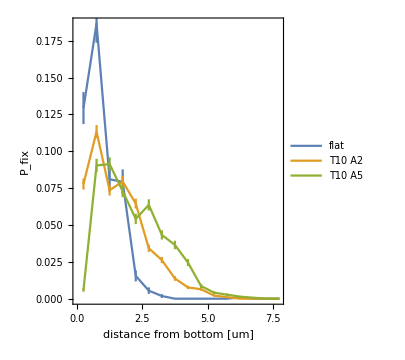

```mathematica
ErrorListPlot[pfix,Joined->True,Frame->True,FrameLabel->{"distance from bottom [um]","P_fix"},BaseStyle->FontSize->18,AspectRatio->1.2,ImageSize->300,FrameStyle->AbsoluteThickness[1],PlotLegends->{"flat","T10 A2","T10 A5"}]
```

## Figure S3 EF

```mathematica
Clear[AllelesEndPoint,AllelesStartPoint]
AllelesEndPoint[name_]:=Module[{names,frames,secsizes},names=FileNames[NotebookDirectory[]<>"\\data_S3EF\\"<>name<>"\\types_*.dat"];
frames=Table[Gather[ReadList[names[[i]],{Number,Number,Number,Number}],(#1[[1]]==#2[[1]])&],{i,Length[names]}];Print[Length[frames]," ",Length[#]&/@frames];
frames=Select[frames,(Length[#]>70)&];(* select only runs that have finished *)
secsizes=Table[1.frames[[i,-1,All,4]],{i,Length[frames]}];
{Mean[1.Length[#]&/@secsizes],SE[1.Length[#]&/@secsizes],Mean[Flatten[secsizes]]/Mean[Total[#]&/@(secsizes)],SE[Flatten[1.secsizes]]/Mean[Total[#]&/@(secsizes)]}
]
AllelesStartPoint[name_]:=Module[{names,frames,secsizes},names=FileNames[NotebookDirectory[]<>"\\data_S3EF\\"<>name<>"\\types_*.dat"];
frames=Table[Gather[ReadList[names[[i]],{Number,Number,Number,Number}],(#1[[1]]==#2[[1]])&],{i,Length[names]}];Print[Length[frames]," ",Length[#]&/@frames];
secsizes=Table[1.frames[[i,1,All,4]],{i,Length[frames]}];
{Mean[1.Length[#]&/@secsizes],SE[1.Length[#]&/@secsizes],Mean[Flatten[secsizes]]/Mean[Total[#]&/@(secsizes)],SE[Flatten[1.secsizes]]/Mean[Total[#]&/@(secsizes)]}
]
```

```mathematica
datasetnames={"100x110_multtypes_no_adh_no_sel_f001_P10_A0","100x110_multtypes_no_adh_no_sel_f002_P10_A0","100x110_multtypes_no_adh_no_sel_f005_P10_A0","100x110_multtypes_no_adh_no_sel_f01_P10_A0","100x110_multtypes_no_adh_no_sel_f02_P10_A0"};
```

```mathematica
alls=AllelesEndPoint[#]&/@datasetnames
```

59 {72,72,72,72,72,72,73,72,73,72,73,72,72,73,72,73,73,73,73,51,72,73,73,72,73,73,73,72,73,34,72,73,73,73,73,73,73,72,12,73,72,72,72,72,73,73,72,73,72,72,72,72,72,72,72,73,73,72,73}

58 {72,72,73,72,72,72,72,73,73,41,72,73,72,73,73,73,72,73,72,24,73,73,73,72,72,73,73,72,54,72,73,72,73,73,72,72,72,73,37,72,72,73,72,73,73,72,73,69,72,72,73,72,73,72,73,72,72,72}

55 {72,72,72,73,73,72,73,73,66,72,72,73,73,72,73,72,73,36,72,73,72,73,73,72,72,73,26,73,73,72,72,73,73,73,73,6,73,72,72,72,72,73,73,73,73,72,73,72,73,72,72,73,73,73,11}

56 {73,72,73,72,72,72,72,72,72,73,72,72,72,73,73,73,73,73,19,72,73,72,73,72,73,72,72,72,53,73,72,73,72,73,72,72,72,73,17,73,73,72,73,73,73,56,73,72,73,73,72,72,73,73,72,37}

45 {73,73,73,72,72,72,24,73,72,72,72,73,72,72,24,73,72,72,73,72,73,72,69,72,72,73,72,73,73,57,73,73,73,72,73,72,64,72,72,72,73,73,73,73,53}

{{4.05357,0.117936,0.246696,0.0116454},{4.15094,0.105702,0.240909,0.0107879},{4.3,0.125357,0.232558,0.0105093},{4.41176,0.134824,0.226667,0.010694},{4.53846,0.175589,0.220339,0.0120066}}

```mathematica
allini=AllelesStartPoint[#]&/@datasetnames
```

59 {72,72,72,72,72,72,73,72,73,72,73,72,72,73,72,73,73,73,73,51,72,73,73,72,73,73,73,72,73,34,72,73,73,73,73,73,73,72,12,73,72,72,72,72,73,73,72,73,72,72,72,72,72,72,72,73,73,72,73}

58 {72,72,73,72,72,72,72,73,73,41,72,73,72,73,73,73,72,73,72,24,73,73,73,72,72,73,73,72,54,72,73,72,73,73,72,72,72,73,37,72,72,73,72,73,73,72,73,69,72,72,73,72,73,72,73,72,72,72}

55 {72,72,72,73,73,72,73,73,66,72,72,73,73,72,73,72,73,36,72,73,72,73,73,72,72,73,26,73,73,72,72,73,73,73,73,6,73,72,72,72,72,73,73,73,73,72,73,72,73,72,72,73,73,73,11}

56 {73,72,73,72,72,72,72,72,72,73,72,72,72,73,73,73,73,73,19,72,73,72,73,72,73,72,72,72,53,73,72,73,72,73,72,72,72,73,17,73,73,72,73,73,73,56,73,72,73,73,72,72,73,73,72,37}

45 {73,73,73,72,72,72,24,73,72,72,72,73,72,72,24,73,72,72,73,72,73,72,69,72,72,73,72,73,73,57,73,73,73,72,73,72,64,72,72,72,73,73,73,73,53}

{{102.203,0.454717,0.00978441,0.},{204.397,0.75927,0.00489245,0.},{509.382,1.45006,0.00196316,0.},{1018.29,2.69845,0.000982043,0.},{2030.47,6.71908,0.000492498,0.}}

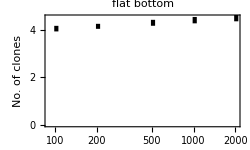

```mathematica
ErrorListLogLinearPlot[Table[{{allini[[i,1]],alls[[i,1]]},ErrorBar[allini[[i,2]],alls[[i,2]]]},{i,Length[alls]}],PlotRange->{0,All},BaseStyle->{FontSize->16},PlotStyle->{Black,AbsolutePointSize[1],AbsoluteThickness[3]},Frame->True,FrameLabel->{"N_initial","No. of clones"},ImageSize->250,AspectRatio->0.6,PlotLabel->"flat bottom"]
```

```mathematica
datasetnames={"100x110_multtypes_no_adh_no_sel_f001_P10_A1.3","100x110_multtypes_no_adh_no_sel_f002_P10_A1.3","100x110_multtypes_no_adh_no_sel_f005_P10_A1.3","100x110_multtypes_no_adh_no_sel_f01_P10_A1.3","100x110_multtypes_no_adh_no_sel_f02_P10_A1.3"};
```

```mathematica
alls=AllelesEndPoint[#]&/@datasetnames
allini=AllelesStartPoint[#]&/@datasetnames
```

60 {72,73,72,72,73,73,73,72,72,72,72,72,73,73,72,72,72,73,73,73,72,72,72,72,72,72,72,73,72,72,72,72,72,72,73,73,72,72,73,72,73,73,72,73,72,72,73,72,72,72,73,72,73,72,73,72,73,72,73,25}

59 {73,73,72,72,72,72,72,73,73,72,72,72,72,72,72,73,72,72,73,72,72,72,73,72,72,73,72,72,73,54,72,73,72,73,73,72,72,73,72,67,72,73,73,73,73,73,72,72,44,72,73,72,73,72,73,73,72,72,72}

58 {73,73,72,72,72,73,72,72,73,20,72,72,72,73,72,72,73,72,72,72,72,72,72,72,72,72,73,72,72,72,72,73,73,72,73,73,72,73,57,73,72,73,73,72,72,73,72,72,73,72,72,73,73,73,73,72,73,65}

57 {72,73,73,72,73,73,73,72,73,73,72,72,72,73,72,72,72,72,73,72,72,73,73,73,73,73,10,73,72,73,72,72,72,73,73,72,45,73,72,73,73,72,73,72,72,72,20,73,72,73,72,73,73,72,72,72,72}

49 {72,72,72,73,73,72,73,72,54,72,73,73,72,72,72,72,65,73,73,73,72,73,73,5,73,72,72,72,72,72,72,72,73,25,73,73,73,72,72,72,62,72,73,73,72,72,73,73,47}

{{6.25424,0.131514,0.159892,0.00493179},{7.32143,0.16138,0.136585,0.00432211},{8.29091,0.14833,0.120614,0.00347592},{8.75926,0.184923,0.114165,0.00329048},{8.88372,0.167085,0.112565,0.00379865}}

60 {72,73,72,72,73,73,73,72,72,72,72,72,73,73,72,72,72,73,73,73,72,72,72,72,72,72,72,73,72,72,72,72,72,72,73,73,72,72,73,72,73,73,72,73,72,72,73,72,72,72,73,72,73,72,73,72,73,72,73,25}

59 {73,73,72,72,72,72,72,73,73,72,72,72,72,72,72,73,72,72,73,72,72,72,73,72,72,73,72,72,73,54,72,73,72,73,73,72,72,73,72,67,72,73,73,73,73,73,72,72,44,72,73,72,73,72,73,73,72,72,72}

58 {73,73,72,72,72,73,72,72,73,20,72,72,72,73,72,72,73,72,72,72,72,72,72,72,72,72,73,72,72,72,72,73,73,72,73,73,72,73,57,73,72,73,73,72,72,73,72,72,73,72,72,73,73,73,73,72,73,65}

57 {72,73,73,72,73,73,73,72,73,73,72,72,72,73,72,72,72,72,73,72,72,73,73,73,73,73,10,73,72,73,72,72,72,73,73,72,45,73,72,73,73,72,73,72,72,72,20,73,72,73,72,73,73,72,72,72,72}

49 {72,72,72,73,73,72,73,72,54,72,73,73,72,72,72,72,65,73,73,73,72,73,73,5,73,72,72,72,72,72,72,72,73,25,73,73,73,72,72,72,62,72,73,73,72,72,73,73,47}

{{101.817,0.439884,0.00982157,0.},{204.407,0.791952,0.00489221,0.},{508.897,1.50029,0.00196504,0.},{1020.25,3.67801,0.000980156,0.},{2030.04,7.07203,0.000492601,0.}}

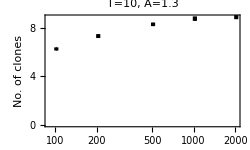

```mathematica
ErrorListLogLinearPlot[Table[{{allini[[i,1]],alls[[i,1]]},ErrorBar[allini[[i,2]],alls[[i,2]]]},{i,Length[alls]}],PlotRange->{0,All},BaseStyle->{FontSize->16},PlotStyle->{Black,AbsolutePointSize[1],AbsoluteThickness[3]},Frame->True,FrameLabel->{"N_initial","No. of clones"},ImageSize->250,AspectRatio->0.6,PlotLabel->"T=10, A=1.3"]
```